Import Data

```mathematica
streckeEbene = 27.3;
```

```mathematica
dataEbene = SemanticImport["/home/dima/Dropbox/AAA_Studium/Master/Semester1/Modellbildung_und_Simulation/Gruppe/hm-modellbildung/angabe1/data/2017/Messungen_2017_Geschwindigkeit_Ebene.csv"]
```

Dataset[<>]

```mathematica
dataEbeneMitGeschw = dataEbene[All,Append[#,"Geschwindigkeit"->streckeEbene /#Zeit]&]
```

Dataset[<>]

## Histogramm

Es wird ein Histogramm erstellt und einer Normalverteilung gegenübergestellt. Für die Kurver der Normalverteilung muss der Erwartungswert und die Standardabweichung berechnet werden.

Berechnung des Mittelwertes und der Standardabweichung

```mathematica
geschwMean = Mean[dataEbeneMitGeschw[All, "Geschwindigkeit"]]
```

1.48076

```mathematica
geschwDeviation = StandardDeviation[dataEbeneMitGeschw[All, "Geschwindigkeit"]]
```

0.144116

Gegenüberstellung von Häufigkeitsverteilung und Normalverteilung. 
ACHTUNG: Das Histogramm wurde mit der Option “PDF” erstellt. Das bedeutet, dass nicht die absoluten Häufigkeiten sondern die Häufigkeitsdichte dargstellt ist, Damit lässt es sich besser mit dem Graphen der Normalverteilung vergleichen. Die Darstellung ist dann nicht mehr von der Anzahl der säulen abhängig.
Bemerkungen wie getrödelt wurden ignoriert. Es wird angenommen, dass im Schnitt es immer Personen gibt, die langsamer oder schneller gehen. Die Probanden hatten keine Vorgabe eine bestimmte Geschwindigkeit einzuhalten. Somit sind auch Probanden zu berücksichtigen, die langsamer gehen. Es ist jedoch anzumerken, dass bei einem Versuch mit nur einer geringen Anzahl von Probanden, solche Sonderheiten eventuell eine signifikante Abweichung verursachen.

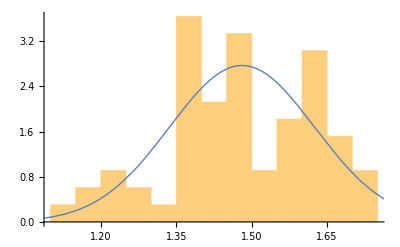

```mathematica
Show[Histogram[dataEbeneMitGeschw[All, "Geschwindigkeit"],10, "PDF"],Plot[PDF[NormalDistribution[geschwMean,geschwDeviation],x],{x,0,2},PlotStyle->Thick]]
```